```mathematica
dmkpluspi00pfunct[m_,ep_]:=493/Sqrt[(m/2)^2-493^2]*(InterpolatingFunction[…][m/(2*493)*ep*(1+Sqrt[1-(2*493/m)^2])]-InterpolatingFunction[…][m/(2*493)*ep*(1-Sqrt[1-(2*493/m)^2])])
```

```mathematica
dmkpluspi2body0pfunct[m_,ep_]:=493/Sqrt[(m/2)^2-493^2]*(InterpolatingFunction[…][m/(2*493)*ep*(1+Sqrt[1-(2*493/m)^2])]-InterpolatingFunction[…][m/(2*493)*ep*(1-Sqrt[1-(2*493/m)^2])])
```

```mathematica
dmkplusleptefunct[m_,ep_]:=493/Sqrt[(m/2)^2-493^2]*(InterpolatingFunction[…][m/(2*493)*ep*(1+Sqrt[1-(2*493/m)^2])]-InterpolatingFunction[…][m/(2*493)*ep*(1-Sqrt[1-(2*493/m)^2])])
```

```mathematica
dmkplusleptmufunct[m_,ep_]:=493/Sqrt[(m/2)^2-493^2]*(InterpolatingFunction[…][m/(2*493)*ep*(1+Sqrt[1-(2*493/m)^2])]-InterpolatingFunction[…][m/(2*493)*ep*(1-Sqrt[1-(2*493/m)^2])])
```

```mathematica
normfunc[dmm_,f_,ep_]:=NIntegrate[(f),{ep,0,dmm}]
```

```mathematica
dmkpluspi00pnorma[dmm_,ep_]:=(((4*0.017)/Quiet[normfunc[dmm,dmkpluspi00pfunct[dmm,ep],ep]])*dmkpluspi00pfunct[dmm,ep])
```

```mathematica
dmkpluspi2body0pnorma[dmm_,ep_]:=(((2*0.207)/Quiet[normfunc[dmm,dmkpluspi2body0pfunct[dmm,ep],ep]])*dmkpluspi2body0pfunct[dmm,ep])
```

```mathematica
dmkplusleptenorma[dmm_,ep_]:=(((2*0.05)/Quiet[normfunc[dmm,dmkplusleptefunct[dmm,ep],ep]])*dmkplusleptefunct[dmm,ep])
```

```mathematica
dmkplusleptmunorma[dmm_,ep_]:=(((2*0.034)/Quiet[normfunc[dmm,dmkplusleptmufunct[dmm,ep],ep]])*dmkplusleptmufunct[dmm,ep])
```

```mathematica
kplusminus[m_,emax_]:=Quiet[Plot[{Evaluate[dmkpluspi00pnorma[m,ep]],Evaluate[dmkpluspi2body0pnorma[m,ep]],Evaluate[dmkplusleptenorma[m,ep]],Evaluate[dmkplusleptmunorma[m,ep]],Evaluate[dmkpluspi00pnorma[m,ep]+dmkpluspi2body0pnorma[m,ep]+dmkplusleptenorma[m,ep]+dmkplusleptmunorma[m,ep]]},{ep,0,emax},PlotRange->Full,PlotStyle->  {Red,Blue,Green,Magenta,Black},PlotLegends->{"K+ -> π+π0π0","K+ -> π+π0","K+ -> e ν π0","K+ -> μ ν π0","1/2 Total K+ K-"},PlotLabel->m "MeV Dark Matter -> K+ K- Photon Spectrum" ]]
```

```mathematica
justtotalpm[m_]:=Quiet[Plot[Evaluate[dmkpluspi00pnorma[m,ep]+dmkpluspi2body0pnorma[m,ep]+dmkplusleptenorma[m,ep]+dmkplusleptmunorma[m,ep]],{ep,0,m},PlotRange->Full,PlotLegends-> {m "MeV"},PlotStyle->RandomColor[]]]
```

```mathematica
totalspreadpm[mlist_,x_]:=Show[(justtotalpm[#])&/@mlist,PlotRange-> {{0,x},Full}]
```

```mathematica
kfile[m_,ep_] :=
dmkpluspi00pfunct[m,ep]+dmkpluspi2body0pfunct[m,ep]+dmkplusleptefunct[m,ep]+dmkplusleptmufunct[m,ep]
```

```mathematica
elist=N@Subdivide[0.01,450,200]
dataset={elist,kfile[1200, elist]}
SetDirectory@NotebookDirectory[]
Export["K+- PDFs\sdfg.csv",dataset, "CSV"]
```

{0.01,2.25995,4.5099,6.75985,9.0098,11.2598,13.5097,15.7597,18.0096,20.2596,22.5095,24.7595,27.0094,29.2594,31.5093,33.7593,36.0092,38.2592,40.5091,42.7591,45.009,47.259,49.5089,51.7589,54.0088,56.2588,58.5087,60.7587,63.0086,65.2586,67.5085,69.7585,72.0084,74.2584,76.5083,78.7583,81.0082,83.2582,85.5081,87.7581,90.008,92.258,94.5079,96.7579,99.0078,101.258,103.508,105.758,108.008,110.258,112.508,114.757,117.007,119.257,121.507,123.757,126.007,128.257,130.507,132.757,135.007,137.257,139.507,141.757,144.007,146.257,148.507,150.757,153.007,155.257,157.507,159.756,162.006,164.256,166.506,168.756,171.006,173.256,175.506,177.756,180.006,182.256,184.506,186.756,189.006,191.256,193.506,195.756,198.006,200.256,202.506,204.755,207.005,209.255,211.505,213.755,216.005,218.255,220.505,222.755,225.005,227.255,229.505,231.755,234.005,236.255,238.505,240.755,243.005,245.255,247.505,249.754,252.004,254.254,256.504,258.754,261.004,263.254,265.504,267.754,270.004,272.254,274.504,276.754,279.004,281.254,283.504,285.754,288.004,290.254,292.504,294.753,297.003,299.253,301.503,303.753,306.003,308.253,310.503,312.753,315.003,317.253,319.503,321.753,324.003,326.253,328.503,330.753,333.003,335.253,337.503,339.752,342.002,344.252,346.502,348.752,351.002,353.252,355.502,357.752,360.002,362.252,364.502,366.752,369.002,371.252,373.502,375.752,378.002,380.252,382.502,384.751,387.001,389.251,391.501,393.751,396.001,398.251,400.501,402.751,405.001,407.251,409.501,411.751,414.001,416.251,418.501,420.751,423.001,425.251,427.501,429.75,432.,434.25,436.5,438.75,441.,443.25,445.5,447.75,450.}

InterpolatingFunction::dmval: Input value {180.577} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {184.876} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {189.175} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.01,2.25995,4.5099,6.75985,9.0098,11.2598,13.5097,15.7597,18.0096,20.2596,22.5095,24.7595,27.0094,29.2594,31.5093,33.7593,36.0092,38.2592,40.5091,42.7591,45.009,47.259,49.5089,51.7589,54.0088,56.2588,58.5087,60.7587,63.0086,65.2586,67.5085,69.7585,72.0084,74.2584,76.5083,78.7583,81.0082,83.2582,85.5081,87.7581,90.008,92.258,94.5079,96.7579,99.0078,101.258,103.508,105.758,108.008,110.258,112.508,114.757,117.007,119.257,121.507,123.757,126.007,128.257,130.507,132.757,135.007,137.257,139.507,141.757,144.007,146.257,148.507,150.757,153.007,155.257,157.507,159.756,162.006,164.256,166.506,168.756,171.006,173.256,175.506,177.756,180.006,182.256,184.506,186.756,189.006,191.256,193.506,195.756,198.006,200.256,202.506,204.755,207.005,209.255,211.505,213.755,216.005,218.255,220.505,222.755,225.005,227.255,229.505,231.755,234.005,236.255,238.505,240.755,243.005,245.255,247.505,249.754,252.004,254.254,256.504,258.754,261.004,263.254,265.504,267.754,270.004,272.254,274.504,276.754,279.004,281.254,283.504,285.754,288.004,290.254,292.504,294.753,297.003,299.253,301.503,303.753,306.003,308.253,310.503,312.753,315.003,317.253,319.503,321.753,324.003,326.253,328.503,330.753,333.003,335.253,337.503,339.752,342.002,344.252,346.502,348.752,351.002,353.252,355.502,357.752,360.002,362.252,364.502,366.752,369.002,371.252,373.502,375.752,378.002,380.252,382.502,384.751,387.001,389.251,391.501,393.751,396.001,398.251,400.501,402.751,405.001,407.251,409.501,411.751,414.001,416.251,418.501,420.751,423.001,425.251,427.501,429.75,432.,434.25,436.5,438.75,441.,443.25,445.5,447.75,450.},{0.,0.,0.,0.,-1.26616×10^-9,0.000651556,0.00353677,0.00675437,0.0106305,0.0144511,0.0180862,0.0214865,0.0246461,0.0275789,0.0303062,0.0328502,0.0352315,0.0374646,0.0391384,0.0402961,0.0414012,0.0424058,0.0433144,0.0441314,0.044866,0.0453206,0.0456333,0.0458658,0.0460231,0.0461125,0.0461409,0.046114,0.046037,0.0459146,0.045751,0.0455499,0.0453148,0.0450489,0.044658,0.0442079,0.043751,0.043289,0.0428232,0.0423552,0.0418861,0.0414172,0.0409496,0.0404843,0.0400222,0.0395644,0.0391115,0.0386644,0.0382235,0.037643,0.0369536,0.0362766,0.0356116,0.0349584,0.0343165,0.0336856,0.0330654,0.0324555,0.0318557,0.0312656,0.030685,0.0301136,0.0295512,0.0289975,0.0284524,0.0279156,0.0273869,0.0268662,0.0263532,0.0258478,0.0253499,0.0248593,0.0243758,0.0238994,0.0234299,0.0229672,0.0225112,0.0220618,0.0216188,0.0211822,0.0207519,0.0203278,0.0199099,0.0194979,0.019092,0.0186919,0.0182977,0.0179092,0.0175264,0.0171492,0.0167776,0.0164115,0.0160509,0.0156956,0.0153457,0.0150011,0.0146617,0.0143276,0.0139985,0.0136745,0.0133555,0.0130416,0.0127325,0.0124284,0.0121291,0.0118345,0.0115448,0.0112597,0.0109792,0.0107034,0.0104321,0.0101653,0.00990295,0.00964502,0.00939145,0.00914219,0.00889719,0.0086564,0.00841978,0.00818727,0.00795883,0.0077344,0.00751393,0.00729738,0.00708469,0.00687581,0.00667069,0.00646928,0.00627152,0.00607737,0.00588677,0.00569967,0.0055148,0.00536353,0.00522728,0.00509214,0.00495899,0.00482782,0.00469857,0.00457121,0.00444572,0.00432204,0.00420016,0.00408003,0.00396162,0.00384489,0.00372982,0.00361636,0.00350448,0.00339416,0.00328534,0.00317801,0.00307212,0.00296765,0.00286456,0.00276282,0.00266239,0.00256324,0.00246535,0.00236867,0.00227318,0.00217884,0.00208563,0.00199351,0.00190246,0.00181243,0.00172341,0.00163537,0.00154826,0.00146207,0.00137677,0.00129233,0.00120872,0.00112591,0.00104388,0.000962602,0.000882048,0.000802194,0.000723016,0.000644488,0.000566588,0.000489292,0.000412577,0.000336422,0.000260805,0.000185705,0.000111248,0.0000338124,-2.92902×10^-6,3.22859×10^-7,8.88908×10^-8,3.87289×10^-8,1.31784×10^-8,2.89142×10^-9,2.96353×10^-10,4.67899×10^-12,-2.00478×10^-12}}

C:\Users\Jacob\Desktop\EtaPion

K+- PDFs\sdfg.csv

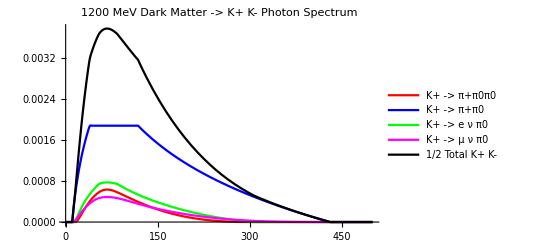

```mathematica
kplusminus[1200,500]
```

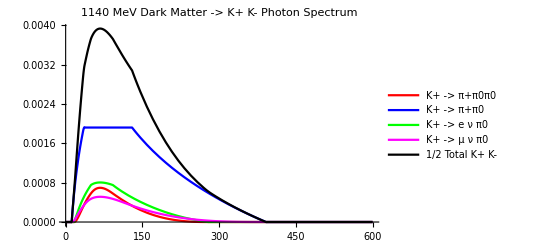

```mathematica
kplusminus[1140,600]
```

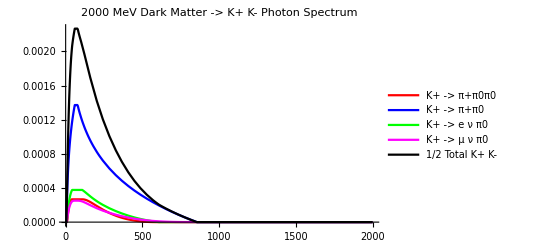

```mathematica
kplusminus[2000,2000]
```

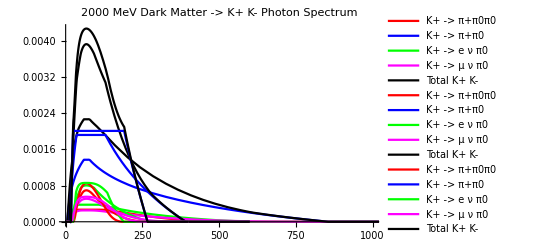

```mathematica
Show[{Out[752],Out[751],Out[750]}, PlotRange-> {{0,1000},Full}]
```

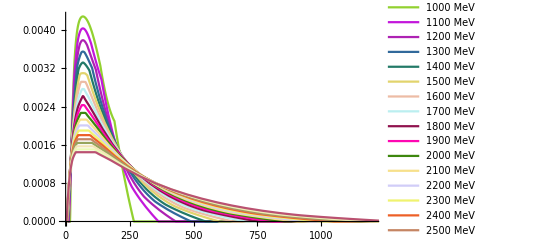

```mathematica
totalspreadpm[Table[1000+100*(i-1),{i,20}],1200]
```